# Introduction to Wolfram Mathematica

The goal of this introduction is to give a brief overwiew of the kinds of operations Mathematica can be used for. This tutorial is far from complete, but it covers some of the basics that should help you get started. Mathematica offers a lot of very powerful constructions and functionality beyond what is covered here.

## Notebooks

The files to which you write Mathematica code and over which you interact with the Mathematica Kernel are called Notebooks. This file here is one. Notebooks have the ending .nb. It is possible to launch Mathematica from the command line, too, in which case you interact more directly with the Kernel.

A Notebook is basically a series of “cells”, where cells can be of different types, e.g. input cells, output cells, text cells, or cells with display formula, items, lists, etc.

This organisation allows you to interleave text, comments and code, which can be very helpful.

Onle cells of type “Input” and “Code” can actually be evaluated by the Kernel. To evaluate a cell of one of these types, place the curser into this cell and then press the Shift+Return key combination. The result is then presented in a cell of the type “Output” just below the input cell you evaluated.

Mathematica can be used to write manuscripts (there is an export function to LATEX) or presentations, and it offers a number of interective features. We are not going to discuss these here, though.

On the right-hand side of a Notebook, there are vertical bars, which represent the hierarchical structure of cells and groups of cells such as subsections, sections, chapters, etc. By klicking on these bars, you can collapse or expand respective levels.

Amont input cells, there are two types. “Normal” input cells are evaluated only if you put your cursor there and press the Shift+Return combination. “Intitialization Cells”, however, are evaluated automatically when you choose “Evaluate Initialization Cells” from the “Evaluation” Menu. It is a good idea to place code such as function or variable definitions into initialization cells. However, calculations that need a lot of time or are more of a “scratch” type should not be assigned to initialization cells.

As a final remark, coding in Mathematica may seem a bit awkward if you use it the first time. I strongly recommend using the different “Assistants” available in the “Palettes” Menu. These offer, for example, easy access to greek letters or constructions like matrices, differentials, fractions, etc. There are short-cuts for these, which you will be picking up as you go. The more you use Mathematica, the more you will find yourself usint the short-cuts instead of the assistant palletes.

Depending on which “Stylesheet” (Menu Format) you use, the default cell type varies. If you use the “Default” Stylesheed, then a new cell is typically an input cell. You can change the type of a cell in the Menu Format/Style.

In an input cell, you can comment out code or text by surrounding it by surrounding it with brackets and asterisks. Example: (* This is my comment *).

## Basics

### Getting help

You can access the documentation to any Mathematica command by typing “?Command”; this provides a short summary with a link to the full documentation page:

```mathematica
?Sin
```

Sin[z] gives the sine of z.

A more detailed summary is given if you type two question marks :

```mathematica
??Sin
```

Sin[z] gives the sine of z.

Attributes[Sin]={Listable,NumericFunction,Protected}

### Variables and assignments

You can use (almost) any variable name (it cannot start with a number and cannot have subscripts), and you can assign numerical expressions (e.g. a real number) or symbolic expressions (e.g. another variable or a function) to a variable name.

There are two types of assignment: direct and delayed assignment. The direct assignment assigns the value to a variable once, namely when you execute the respective cell, and then the variable keeps this value until you assign a different value to it. In contrast, if you use the delayed assignment, then Mathematica just keeps in mind the symbolic expression you assigned to the variable, but only evaluates it when the variable is actually used.

Direct assignment using “=”:

```mathematica
(* Directly assigning 5 to a *)
a=5
```

5

```mathematica
(* b is now a, which is 5, so b is 5 *)
b=a
```

5

```mathematica
(* Assign a new value to a *)
a=10
```

10

```mathematica
(* Note that b is still 5 *)
```

```mathematica
b
```

5

Delayed assignment using “:=”:

```mathematica
(* Directly assigning 5 to a *)
a=5
```

5

```mathematica
(* Now we assign a to c, but the assignment is now delayed! *)
c:=a
```

```mathematica
(* Assign a new value to a *)
a=10
```

10

```mathematica
(* Note that c takes the current value of a, not the one that a had when c was defined, which ws 5! *)
```

```mathematica
c
```

10

Sometimes you want to “clear” variables of their assignments. This is done as follows:

```mathematica
a
```

12

```mathematica
Clear[a,b,c]
```

```mathematica
a
```

a

```mathematica
b
```

b

```mathematica
c
```

c

### Basic operations

Summation, substraction, multiplication, and division:

```mathematica
a+b
```

a+b

```mathematica
8-b
```

8-b

```mathematica
3.8*2
```

7.6

Instead of a “*” you an also use a space for multiplication. If you put a space between two numbers, Mathematica will automatically put a “×” in there. For symbolic variables, the space is sufficient.

```mathematica
3.8 2
```

```mathematica
x y
```

x y

```mathematica
x*y
```

x y

```mathematica
a/c+9-2*3
```

3+a/c

Powers:

```mathematica
x^a
```

x^a

```mathematica
b^2
```

b^2

Roots:

```mathematica
Sqrt[4]
```

2

```mathematica
(a^8)^(1/4)
```

144

Exponentials:

```mathematica
Exp[x]
```

ⅇ^x

Alternatively, we can type

```mathematica
ⅇ^(-a x+b)
```

ⅇ^(b-a x)

The double-stroke ⅇ can be obtained by typing “Esc + e + e + Esc”. The escape key Esc is the gate to many short-cuts. Another example are Greek letters. To obtain the first three letters of the Greek alphabet, type “Esc + a + Esc”, “Esc + b + Esc”, and “Esc + g + Esc” to obtain α, β, and γ. To write letters in double-stroke font, such as 𝔼, use “Esc + dsE + Esc”. Similarly, for letters in script shape, such as 𝒜, use “Esc + scA + Esc”.

### Manipulating expressions

Expanding a product:

```mathematica
Expand[a(b+c)-a(e-f)]
```

a b+a c-a e+a f

Alternatively, you can put the command after the expression, using “//”:

```mathematica
a(b+c)-a(e-f)//Expand
```

a b+a c-a e+a f

```mathematica
?Expand
```

Expand[expr] expands out products and positive integer powers in expr. 
Expand[expr,patt] leaves unexpanded any parts of expr that are free of the pattern patt.

Factoring an expression:

```mathematica
Factor[a+c a-d a-a^2+e a^2]
```

a (1-a+c-d+a e)

```mathematica
?Factor
```

Factor[poly] factors a polynomial over the integers. 
Factor[poly,Modulus→p] factors a polynomial modulo a prime p. 
Factor[poly,Extension→{a_1,a_2,…}] factors a polynomial allowing coefficients that are rational combinations of the algebraic numbers a_i.

Simplifying expressions:

```mathematica
expr1=a/b+a^4-b c+4/b
```

a^4+4/b+a/b-b c

```mathematica
Simplify[expr1]
```

(4+a+a^4 b-b^2 c)/b

```mathematica
FullSimplify[expr1]
```

a^4+(4+a)/b-b c

Again, we can use the alternative “post-fix” notation:

```mathematica
expr1//Simplify
```

(4+a+a^4 b-b^2 c)/b

Sometimes, it is useful to group subterms by a (set of) focal variable(s). This is done using “Collect”:

```mathematica
expr2=a b+(x-z)b+(e+f-g)a
```

a b+a (e+f-g)+b (x-z)

```mathematica
Collect[expr2,b]
```

a (e+f-g)+b (a+x-z)

```mathematica
Collect[expr2,a]
```

a (b+e+f-g)+b (x-z)

```mathematica
Collect[expr2,{a,b}]
```

a (b+e+f-g)+b (x-z)

To determine the degree of a polynomical in a focal variable, use

```mathematica
expr1
```

a^4+4/b+a/b-b c

```mathematica
Exponent[expr1,a]
```

4

### Data structures

There is one atomic data structure, called a List. You can build more complicated structures by nesting lists. E.g., a 2x2 matrix is just a list of two sublists, where each sublist has one element.

```mathematica
myList1={1,2,3,4,5,6,7,8,9,10}
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
myNestedList1={{a,b},{c,d}}
```

{{a,b},{c,d}}

A very efficient way of constructing lists is to use the “Table” command:

```mathematica
Table[i,{i,1,10,1}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[a^x,{x,1,10,1}]
```

{a,a^2,a^3,a^4,a^5,a^6,a^7,a^8,a^9,a^10}

```mathematica
myNestedList2=Table[{x,y},{y,1,5,1},{x,{a,b,c,d,e}}]
```

{{{a,1},{b,1},{c,1},{d,1},{e,1}},{{a,2},{b,2},{c,2},{d,2},{e,2}},{{a,3},{b,3},{c,3},{d,3},{e,3}},{{a,4},{b,4},{c,4},{d,4},{e,4}},{{a,5},{b,5},{c,5},{d,5},{e,5}}}

Use “TableForm” or “MatrixForm” to display lists in a visually more appealing way:

```mathematica
myNestedList2//TableForm
```

a
1 | b
1 | c
1 | d
1 | e
1
a
2 | b
2 | c
2 | d
2 | e
2
a
3 | b
3 | c
3 | d
3 | e
3
a
4 | b
4 | c
4 | d
4 | e
4
a
5 | b
5 | c
5 | d
5 | e
5

```mathematica
MatrixForm[myNestedList2]
```

((a
1) | (b
1) | (c
1) | (d
1) | (e
1)
(a
2) | (b
2) | (c
2) | (d
2) | (e
2)
(a
3) | (b
3) | (c
3) | (d
3) | (e
3)
(a
4) | (b
4) | (c
4) | (d
4) | (e
4)
(a
5) | (b
5) | (c
5) | (d
5) | (e
5))

Accessing elements of lists:

```mathematica
myList1[[3]]
```

3

```mathematica
myList1[[All]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
myList1[[1;;4]]
```

{1,2,3,4}

```mathematica
myList1[[{1,5,6}]]
```

{1,5,6}

```mathematica
myNestedList1[[1]]
```

{a,b}

```mathematica
myNestedList1[[1,2]]
```

b

```mathematica
myNestedList2[[1]]
```

{{a,1},{b,1},{c,1},{d,1},{e,1}}

```mathematica
myNestedList2[[2,4]]
```

{d,2}

```mathematica
myNestedList2[[All,2]]
```

{{b,1},{b,2},{b,3},{b,4},{b,5}}

Counting from the end:

```mathematica
myList1[[-3]]
```

8

```mathematica
myList1[[-6;;-4]]
```

{5,6,7}

Asking for the position of an element in a list:

```mathematica
Position[myList1,3]
```

{{3}}

```mathematica
Position[myNestedList2,{b,2}]
```

{{2,2}}

```mathematica
(* Check: *)
myNestedList2[[2,2]]
```

{b,2}

### Some list manipulations

```mathematica
myNestedList1
```

{{a,b},{c,d}}

```mathematica
Flatten[myNestedList1]
```

{a,b,c,d}

```mathematica
myNestedList2
```

{{{a,1},{b,1},{c,1},{d,1},{e,1}},{{a,2},{b,2},{c,2},{d,2},{e,2}},{{a,3},{b,3},{c,3},{d,3},{e,3}},{{a,4},{b,4},{c,4},{d,4},{e,4}},{{a,5},{b,5},{c,5},{d,5},{e,5}}}

```mathematica
Flatten[myNestedList2]
```

{a,1,b,1,c,1,d,1,e,1,a,2,b,2,c,2,d,2,e,2,a,3,b,3,c,3,d,3,e,3,a,4,b,4,c,4,d,4,e,4,a,5,b,5,c,5,d,5,e,5}

```mathematica
myList1
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
myList2={a,b,c,d,e,f,g,h,i,j}
```

{a,b,c,d,e,f,g,h,i,j}

```mathematica
Riffle[myList1,myList2]
```

{1,a,2,b,3,c,4,d,5,e,6,f,7,g,8,h,9,i,10,j}

```mathematica
Join[myList1,myList2[[1;;5]]]
```

{1,2,3,4,5,6,7,8,9,10,a,b,c,d,e}

```mathematica
Partition[myList1,2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
Partition[Riffle[myList1,myList2],2]
```

{{1,a},{2,b},{3,c},{4,d},{5,e},{6,f},{7,g},{8,h},{9,i},{10,j}}

```mathematica
myList3={20,4,10,2,4,5}
```

{20,4,10,2,4,5}

```mathematica
Sort[myList3]
```

{2,4,4,5,10,20}

```mathematica
Split[myList1]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}

```mathematica
Split[myList3]
```

{{20},{4},{10},{2},{4},{5}}

```mathematica
Split[Sort[myList3]]
```

{{2},{4,4},{5},{10},{20}}

### Rules and their application

Rules can be used to replace expressions or symbols by another expression at a given point. This allows you to distinguish between “general” expressions and their specific meaning for particular variable/paramter values.

Rules are defined using an arrow “->”:

```mathematica
myRule1:=a->5
```

```mathematica
b=a
```

a

```mathematica
b
```

a

Rules are applied using “/.”:

```mathematica
b/.myRule1
```

5

```mathematica
Sin[x]
```

Sin[x]

```mathematica
Sin[x]/.{x->2π}
```

0

Alternatively, and equivalently, we can use “Replace” to apply the rule:

```mathematica
Replace[b,myRule1]
```

5

### Textual versus short-cut commands

For many commands, there are short-cuts. We have seen an example above: The command “Replace” has the short-cut “./”. Rather than listing all combinations of commands and short-cuts here, we just mention this. You will encounter these pairs in practice early enough.

## Functions

### Function definitions

To define a function that takes arguments, we use the following syntax:

```mathematica
myFunc1[a_,b_,c_]:=a+b/c
```

Note that we use the delayed assignment “:=” here. Moreover, arguments are declared using the so-called pattern “x_”, which stands for “any expression, to be referred to as x”. It often makes sense to place functions in an “initialization cell”, so that they are defined whenever the Notebook is initialised.

We can then use the function as follows:

```mathematica
myFunc1[1,4,3]
```

7/3

Another example:

```mathematica
myFunc2[x_]:=α x^2+β x+γ
```

In this case, we define the function as a function of x, with parameters α, β, and γ to be defined when we use the function:

```mathematica
myFunc2[x]
```

x^2 α+x β+γ

```mathematica
myFunc2[x]/.{α->1,β->2,γ->4}
```

4+2 x+x^2

### Recursions

Recursion equations are, in most cases, best defined using the construction “f[x_]:=f[x]=expression including (x-1)”, in combination with the definition of f[0]. The advantage of this construction is that the function is computed once for every x and these values are then remembered. However, this only pays off if we initially assign specific numeric values to any of the parameters that are part of “expression including (x-1)”.

For instance, the recursion equation for the logistic model of growth in discrete time can be implemented as follows:

```mathematica
Clear[n]
n0=10;
myr=0.5;
myΚ=1000;
n[t_]:=n[t]= n[t-1]+myr n[t-1](1-n[t-1]/myΚ)
n[0]=n0;
```

```mathematica
n[0]
```

10

```mathematica
n[1]
```

14.95

```mathematica
n[100]
```

1000.

```mathematica
n[2000]
```

Hold[n[978-1]+myr n[978-1] (1-n[978-1]/myΚ)]

Mathematica by default sets the recursion limit to 1024 to prevent unintended infinite loops. To navigate around this, you can set this recursion limit to infinity. It is a good idea to do this locally in a so-called “Block”:

```mathematica
Block[{$RecursionLimit=Infinity},n[2000]]
```

1000.

As another example, consider the diploid model of natural selection in discrete time:

```mathematica
Clear[p]
p0=0.01;
myW11=1;
myW12=1-h s/.{h->0.5,s->0.05};
myW22=1-s/.{s->0.05};
p[t_]:=p[t]=p[t-1](p[t-1]myW11+(1-p[t-1])myW12)/(p[t-1]^2 myW11+2p[t-1](1-p[t-1])myW12+(1-p[t-1])^2 myW22)
p[0]=p0;
```

```mathematica
p[3]
```

0.0108015

```mathematica
p[10]
```

0.0129268

```mathematica
p[100]
```

0.119143

```mathematica
p[1000]
```

1.

### Approximating a function using a Taylor series

A Taylor series of a function can be obtained as follows:

```mathematica
myFunc2[x]
```

x^2 α+x β+γ

A 1st-order Taylor series of “myFunc2” around x=0:

```mathematica
Series[myFunc2[x],{x,0,1}]
```

γ+β x+O[x]^2

```mathematica
Series[myFunc2[x],{x,0,1}]//Normal
```

x β+γ

A 2nd-order Taylor series of a 3rd-order polynomial in x around x=0:

```mathematica
Series[a x^3-b x^2+c x-d,{x,0,1}]
```

-d+c x+O[x]^2

The same, but around x=1:

```mathematica
Series[a x^3-b x^2+c x-d,{x,1,1}]
```

(c-d)+(a+c) (x-1)+O[x-1]^2

```mathematica
Series[a x^3-b x^2+c x-d,{x,0,2}]
```

-d+c x-a x^2+O[x]^3

## Plotting

### Plotting a continuous function



```mathematica
Plot[Sin[ϕ],{ϕ,0,2π}]
```

```mathematica
?myFunc1
```

Global`myFunc1

myFunc1[a_,b_,c_]:=a+b/c

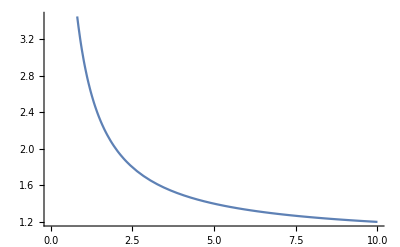

```mathematica
Plot[myFunc1[1,2,c],{c,0,10}]
```

Adding axis labels:

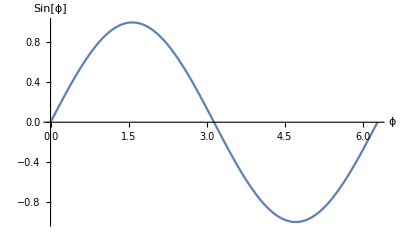

```mathematica
Plot[Sin[ϕ],{ϕ,0,2π},
AxesLabel->{"ϕ","Sin[ϕ]"}
]
```

Increasing the font size for the labels:

```mathematica
Plot[Sin[ϕ],{ϕ,0,2π},
AxesLabel->{"ϕ","Sin[ϕ]"},
LabelStyle->Directive[FontSize->14]
]
```

-Graphics-

Changing the style of the line:

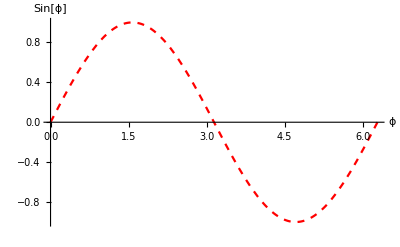

```mathematica
Plot[Sin[ϕ],{ϕ,0,2π},
AxesLabel->{"ϕ","Sin[ϕ]"},
LabelStyle->Directive[FontSize->14],
PlotStyle->{{Red,Dashed}}
]
```

Plotting multiple functions:

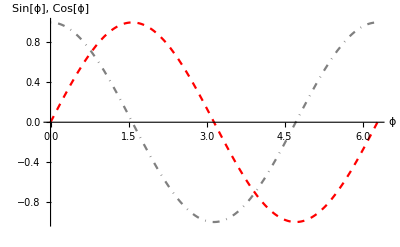

```mathematica
Plot[{Sin[ϕ],Cos[ϕ]},{ϕ,0,2π},
AxesLabel->{"ϕ","Sin[ϕ], Cos[ϕ]"},
LabelStyle->Directive[FontSize->14],
PlotStyle->{{Red,Dashed},{Gray,DotDashed}}
]
```

Changing the plot range and adding a title:

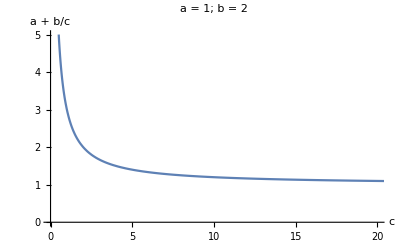

```mathematica
Plot[myFunc1[1,2,c],{c,0,100},
PlotRange->{{0,20},{0,5}},
AxesLabel->{"c","a + b/c"},
PlotLabel->"a = 1; b = 2",
LabelStyle->Directive[FontSize->14]
]
```

Using a frame and annotating the frame edges:

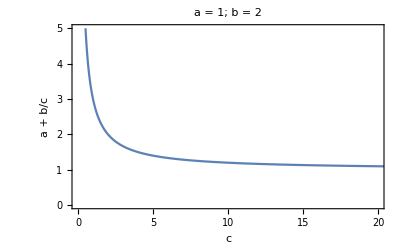

```mathematica
Plot[myFunc1[1,2,c],{c,0,100},
PlotRange->{{0,20},{0,5}},
Frame->True,
FrameLabel->{"c","a + b/c"},
PlotLabel->"a = 1; b = 2",
LabelStyle->Directive[FontSize->14]
]
```

### Plotting discrete points

Let us plot the recursion equation for the discrete-time logistic growth model:

```mathematica
plotData1=Table[{t,n[t]},{t,0,50}]
```

{{0,10},{1,14.95},{2,22.3132},{3,33.2209},{4,49.2796},{5,72.7051},{6,106.415},{7,153.96},{8,219.088},{9,304.632},{10,410.548},{11,531.547},{12,656.05},{13,768.874},{14,857.727},{15,918.743},{16,956.07},{17,977.07},{18,988.272},{19,994.067},{20,997.016},{21,998.504},{22,999.251},{23,999.625},{24,999.812},{25,999.906},{26,999.953},{27,999.977},{28,999.988},{29,999.994},{30,999.997},{31,999.999},{32,999.999},{33,1000.},{34,1000.},{35,1000.},{36,1000.},{37,1000.},{38,1000.},{39,1000.},{40,1000.},{41,1000.},{42,1000.},{43,1000.},{44,1000.},{45,1000.},{46,1000.},{47,1000.},{48,1000.},{49,1000.},{50,1000.}}

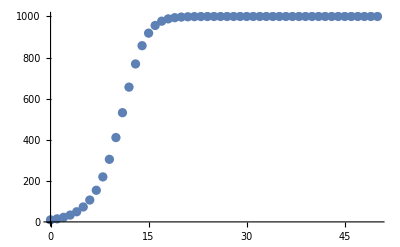

```mathematica
ListPlot[plotData1]
```

Improving the look and annotating the plot:

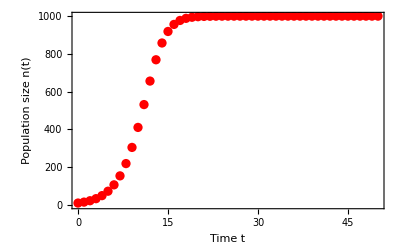

```mathematica
listPlot1=ListPlot[plotData1,
Frame->True,
FrameLabel->{"Time t","Population size n(t)"},
LabelStyle->Directive[FontSize->10],
PlotStyle->Red
]
```

Joining the dots and restricting the plot range along the x axis:

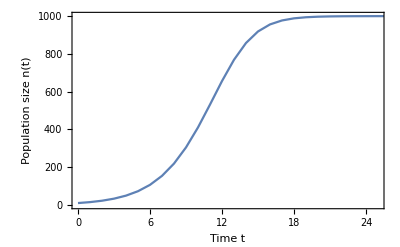

```mathematica
listPlot2=ListPlot[plotData1,
Frame->True,
FrameLabel->{"Time t","Population size n(t)"},
LabelStyle->Directive[FontSize->14],
Joined->True,
PlotRange->{{0,25},Full}
]
```

Combining two plots:

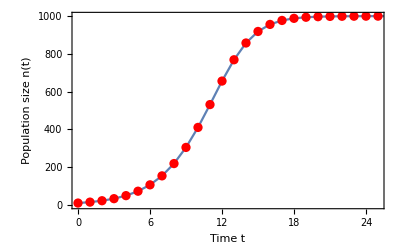

```mathematica
Show[{listPlot2,listPlot1}
]
```

Note that the plot range is adopted from the first plot element in the list given to “Show”, as are other plotting arguments (e.g. the size of the axes labels).

### Contour plots

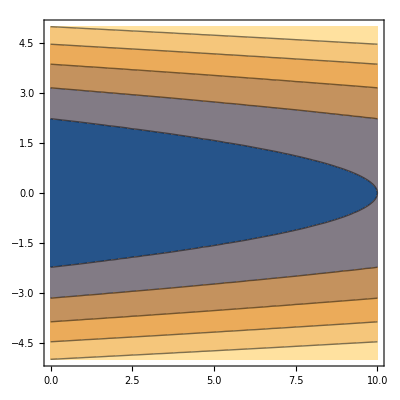

```mathematica
ContourPlot[
x+2 y^2,{x,0,10},{y,-5,5}
]
```

Again some styling:

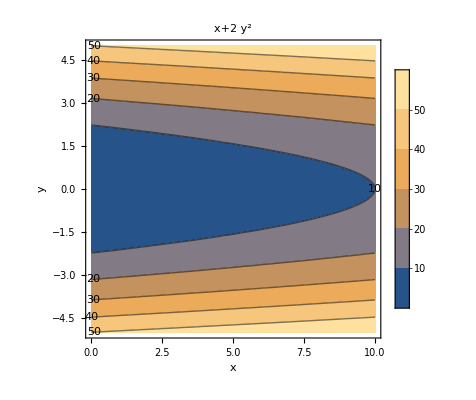

```mathematica
ContourPlot[
x+2 y^2,{x,0,10},{y,-5,5},
FrameLabel->{"x", "y"},
PlotLabel->x+2 y^2,
LabelStyle->Directive[FontSize->18,FontFamily->"Times"],
PlotLegends->Automatic,
ContourLabels->True
]
```

### Interactive plots

Interactive plots can be drawn using “Manipulate”. Although this command can also be used in other contexts, I use it most often when plotting.

```mathematica
Manipulate[
ContourPlot[
x+a y^2,{x,0,10},{y,-5,5},
FrameLabel->{"x", "y"},
PlotLabel->"x + "<>ToString[a]<>" y^2",
LabelStyle->Directive[FontSize->14,FontFamily->"Helvetica Neue"],
PlotLegends->Automatic,
ContourLabels->True
],
{{a,-0.5},-5,5}
]
```

Using the “Manipulate” command in another context:

```mathematica
Manipulate[
x,
{{x,1},-10,10,2}
]
```

Essentially, you can “manipulate” any Mathematica expression. Just be aware of the fact that Mathematica internally pre-computes that expression for the range of variables you indicate. This may be overly costly for complicated expressions!

## Equations

### Solving equations (symbolically and numerically)

First of all, it is time to introduce the “equals” operator “==”, and higlight the difference to the “assignment” operator “=”. Equations are expressed as follows:

```mathematica
a x+c==5
```

c+a x==5

We can also assign an equation to a variable for easier access later on. You can use both the immediate and delayed assignment for this:

```mathematica
myEq1=a x+c==5
```

c+a x==5

```mathematica
myEq1Alt:=a x+c==9
```

```mathematica
myEq1
```

c+a x==5

```mathematica
myEq1Alt
```

c+a x==9

To solve an equation symbolically for a variable of interest (e.g. x here), we use

```mathematica
Solve[a x+c==5,x]
```

{{x→(5-c)/a}}

Mathematica returns a (potentially nested) list representing the set of all solutions it can find.

We can also solve an equation that is accessed as a variable:

```mathematica
Solve[myEq1Alt,x]
```

{{x→(9-c)/a}}

If we try to solve a transcendental equation, Mathematica complains because in general such equations cannot be solved analytically:

```mathematica
Solve[ⅇ^(-a x)+x==b x^2,x]
```

Solve[ⅇ^(-a x)+x==a x^2,x]

```mathematica
Solve[x==ⅇ^(-a x),x]
```

{{x→ProductLog[a]/a}}

However, you can sometimes find (a) numerical solution(s) for a specific set of parameter values using “NSolve”. Let us try this for the transcendental equation we just encountered:

```mathematica
NSolve[x==ⅇ^(-0.5 x),x]
```

{{x→0.703467}}

```mathematica
?NSolve
```

RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to find numerical approximations to the solutions of the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", "Reals"}], "]"}] finds solutions over the domain of real numbers.

### Solving systems of equations

To solve a system of equations, we proceed as follows:

```mathematica
myEq2:=a x +y==c
myEq3:=b x-y==d
```

```mathematica
Solve[{myEq2,myEq3},{x,y}]
```

{{x→-(-c-d)/(2 a),y→(c-d)/2}}

### Using assumptions

Sometimes, it is crucial to tell Mathematica about assumptions you are happy to make. This often allows for much simpler solutions, sometimes it even makes the difference to Mathematica finding a solution at all.

```mathematica
Sqrt[x^2]
```

√(x^2)

```mathematica
Simplify[Sqrt[x^2],Assumptions->{x>0}]
```

x

### Dealing with inequalities

A useful command in the context of inequalities is “Reduce”.

```mathematica
Reduce[{0<x<2,1<x<4},x]
```

1<x<2

```mathematica
Reduce[{x<1,x>3},x]
```

False

Again, telling Mathematica about assumptions you are happy to make can simplify things a lot:

```mathematica
Simplify[Reduce[a x+b x^2<c,x]]
```

x∈Reals&&((c<0&&(((a≠0||√(c/b)<x||√(c/b)+x<0)&&(a==0||b^2 √((a^2+4 b c)/b^2)<b (a+2 b x)||b (a+b (√((a^2+4 b c)/b^2)+2 x))<0)&&b<0)||(b==0&&a≠0&&a x<c)||(a≠0&&b>0&&c (a^2+4 b c)<0&&√((a^2+4 b c)/b^2)>a/b+2 x&&b (a+b (√((a^2+4 b c)/b^2)+2 x))>0)))||(c==0&&(((a≠0||x≠0)&&(a==0||√(a^2/b^2)<a/b+2 x||b (a+b (√(a^2/b^2)+2 x))<0)&&b<0)||(b==0&&((a<0&&x>0)||(a>0&&x<0)))||(a≠0&&b>0&&√(a^2/b^2)>a/b+2 x&&b (a+b (√(a^2/b^2)+2 x))>0)))||(c>0&&((a==0&&((√(c/b)+x>0&&x<√(c/b))||b≤0))||(b==0&&a≠0&&a x<c)||(a≠0&&((4 b+a^2/c==0&&b (a+b (√((a^2+4 b c)/b^2)+2 x))≠0)||(b<0&&c (a^2+4 b c)>0&&(b (a+b (√((a^2+4 b c)/b^2)+2 x))<0||b (a-b √((a^2+4 b c)/b^2)+2 b x)>0))||c (a^2+4 b c)<0||(b>0&&√((a^2+4 b c)/b^2)>a/b+2 x&&b (a+b (√((a^2+4 b c)/b^2)+2 x))>0))))))

Let us tell Mathematica what we are willing to assume about the parameters and variables:

```mathematica
Simplify[Reduce[a x+b x^2<c,x],Assumptions->{c<0,a>0,b>0,x∈Reals}]
```

a^2+4 b c>0&&-(a+√(a^2+4 b c))/(2 b)<x<(-a+√(a^2+4 b c))/(2 b)

## Calculus

### Derivatives

To take the derivative of a function, you either use the prime notation or the command “D”:

```mathematica
myf[x_]:=Sin[x]+x^2
```

```mathematica
myf'[x]
```

2 x+Cos[x]

```mathematica
D[myf[x],x]
```

2 x+Cos[x]

Taking the second derivative:

```mathematica
myf''[x]
```

2-Sin[x]

Or:

```mathematica
D[myf[x],{x,2}]
```

2-Sin[x]

### Integrals

To obtain an indefinite integral, we use

```mathematica
Integrate[2x+Cos[x],x]
```

x^2+Sin[x]

```mathematica
Integrate[myFunc2[x],x]
```

(x^3 α)/3+(x^2 β)/2+x γ

For a definite integral, we have to give the boundaries of integration:

```mathematica
Integrate[2x+Cos[x],{x,0,π}]
```

π^2

```mathematica
Integrate[myFunc2[x],{x,-10,5}]
```

375 α-(75 β)/2+15 γ

Numerical integration is done using “NIntegrate”:

```mathematica
NIntegrate[Sin[Sin[x]],{x,0,2}]
```

1.24706

## Linear algebra

### Writing vectors and matrices

As mentioned above, the universal data structure used by Mathematica are (nested) lists. A vector is therefore represented as a one-dimensional list; a matrix as a nested list of depth 2, i.e. with two levels.

```mathematica
Clear[p]
```

```mathematica
myVec1:={v1,v2,v3}
```

```mathematica
myMat1:={{a,b,c},{d,e,f},{g,h,i}}
myMat2:={{p,q},{r,s},{t,u}}
```

```mathematica
myVec1
```

{v1,v2,v3}

Again, we can use “MatrixForm” or “TableForm” to obtain a more userfriendly display of nested lists:

```mathematica
myVec1//MatrixForm
```

(v1
v2
v3)

```mathematica
myMat1//MatrixForm
```

(a | b | c
d | e | f
g | h | i)

```mathematica
TableForm[myMat1]
```

a | b | c
d | e | f
g | h | i

### Matrix operations

We multiply matrices or vectors using “.”:

```mathematica
myMat1.myMat2
```

{{a p+b r+c t,a q+b s+c u},{d p+e r+f t,d q+e s+f u},{g p+h r+i t,g q+h s+i u}}

```mathematica
%//MatrixForm
```

(a p+b r+c t | a q+b s+c u
d p+e r+f t | d q+e s+f u
g p+h r+i t | g q+h s+i u)

```mathematica
myVec1.myMat1
```

{a v1+d v2+g v3,b v1+e v2+h v3,c v1+f v2+i v3}

The operators “+“, “-“, and “^” work element-wise:

```mathematica
myMat1+3
```

{{3+a,3+b,3+c},{3+d,3+e,3+f},{3+g,3+h,3+i}}

```mathematica
myMat2+myVec1
```

{{p+v1,q+v1},{r+v2,s+v2},{t+v3,u+v3}}

### Determinant, inverse, transpose, trace

```mathematica
Det[myMat1]
```

-c e g+b f g+c d h-a f h-b d i+a e i

```mathematica
Inverse[myMat1]//Simplify
```

{{(f h-e i)/(c e g-b f g-c d h+a f h+b d i-a e i),(c h-b i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(c e-b f)/(c e g-b f g-c d h+a f h+b d i-a e i)},{(f g-d i)/(-c e g+b f g+c d h-a f h-b d i+a e i),(c g-a i)/(c e g-b f g-c d h+a f h+b d i-a e i),(c d-a f)/(-c e g+b f g+c d h-a f h-b d i+a e i)},{(e g-d h)/(c e g-b f g-c d h+a f h+b d i-a e i),(b g-a h)/(-c e g+b f g+c d h-a f h-b d i+a e i),(b d-a e)/(c e g-b f g-c d h+a f h+b d i-a e i)}}

```mathematica
Transpose[myMat1]
```

{{a,d,g},{b,e,h},{c,f,i}}

```mathematica
Tr[myMat1]
```

a+e+i

### Eigenvalues and eigenvectors

```mathematica
Eigenvalues[{{a,b},{c,d}}]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

```mathematica
Eigenvectors[{{a,b},{c,d}}]
```

{{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c),1},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c),1}}

## Example: Analysis of a simple non-linear SI model

Let us consider a simple model of disease with two categories of host individuals: infected ones and those susceptible to the disease. Let the number of infected and susceptible individuals at time t be Y(t) and S(t), respectively. We assume that the population of susceptible hosts is replenished by immigration at a total rate θ, and that recovered individuals immediately become susceptible again, i.e. there is no class of immune or resistant hosts. Further, denote the transition rate of the disease by β. Recall that under the mass-action principle the transition rate is given by the product of the rate of contact, c, between susceptible and infected hosts times the probability of transmission conditional on a contact, a, i.e. β=c a. Last, let d be the per capita background mortality rate of the host, ν the additional mortality caused by infection, and γ the rate of clearance of the disease through defense mechanisms of the host.

### Writing the differential equations

The model can then be described in continuous time by the following pair of differential equations :

ⅆS/ⅆt=θ-d S-β S Y+γ Y,
	ⅆY/ⅆt=β S Y-(d+ν+γ)Y.

Implementing these equations in Mathematica (choosing to call the differential of variable X “XDot”):

```mathematica
SDot:=θ-d S-β S Y-β S Y + γ Y
YDot:=β S Y-(d+ν+γ)Y
```

### Finding the equilibria

To identify the equilibria (Ŝ, Ŷ) of the model, we set ⅆS/ⅆt=0 and  ⅆY/ⅆt=0. This yields the two equilibrium conditions that must be jointly satisfied:

0=θ-d Ŝ-β Ŝ Ŷ+γ Ŷ,
	0=β  Ŝ Ŷ-(d+ν+γ)Ŷ.

In contrast to linear multivariable models, there can now be multiple equilibria for non-linear models. We wish to identify all of them. In practice, this can be a challenging, sometimes impossible talk, as not all solutions to Eq. (2) might be found explicitly. In the case of our example, the solutions can be found by hand by factoring the equations in (2) and looking for values of the variables that make any of the factors equal to 0.

Here, we will use Mathematica to find the solutions and simplify these:

```mathematica
solEq1=Solve[{SDot==0,YDot==0},{S,Y}]//FullSimplify
```

{{S→(d+γ+ν)/β,Y→(β θ-d (d+γ+ν))/(β (2 d+γ+2 ν))},{S→θ/d,Y→0}}

Mathematica returns the solutions in the form of “rules”. The second solution (Ŝ=θ/d, Ŷ=0) corresponds to the case where the disease is absent. The first solution represents the so-called “endemic equilibrium” where the disease is present.

### Assessing stability

TODO: Proceed on p. 299 of the book (starting with the box in the margin).